```mathematica
ClearAll["Global`*"]
<< HPL`;
```

Package HPL already loaded...

$Aborted

Extract equations (B.5) - (B.7) from [Vogt, Moch: “The third-order QCD corrections to deep-inelastic scattering by photon exchange” ,Nucl. Phys. B, 724 (1-2), 3, 2005] with the help of ChatGPT

```mathematica
pqq[x_]:=2/(1-x)-1-x;
pqg[x_]:=1-2 x+2 x^2;
pgq[x_]:=(2 x-1)/(-2+x);
pgg[x_]:=1/(1-x)+1/x-2+x-x^2;

c2ns2[x_]:=CF*(CF-CA/2)*((8/5)*(9*pqg[-x]*(1-x)+pgq[-x]*(1-x^-1)+(37+17*x))*HPL[{-1,0},x]+4*pqq[-x]*(7*Zeta3+6*HPL[{-2,0},x]+4*HPL[{-1,2},x]-8*HPL[{-1,-1,0},x]+10*HPL[{-1,0,0},x]-3*HPL[{0,0,0},x]-8*HPL[{-1},x]*Zeta2-2*HPL[{0},x]+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])-(72/5)*pqg[x]*((1+x)*(Zeta2-HPL[{0,0},x])-1-HPL[{0},x])+(8/5)*pgq[x]*(1-HPL[{0},x])+8*(1-5*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-8*(1+5*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2))+CF*nf*(1/54*pqq[x]*(247-144*Zeta2+180*HPL[{0,0},x]+72*HPL[{1,0},x]+72*HPL[{1,1},x]+342*HPL[{0},x]+174*HPL[{1},x]+144*HPL[{2},x])-1/3*(7+19*x)*HPL[{0},x]-1/3*(1+13*x)*HPL[{1},x]-1/18*(23+243*x)+DiracDelta[1-x]*(457/36+4/3*Zeta3+38/3*Zeta2))+CF^2*(16*HPL[{-2,0},x]+1/5*(33+37*x)*HPL[{0,0},x]+1/4*pqq[x]*(51+128*Zeta3+48*Zeta2+96*HPL[{-2,0},x]-12*HPL[{0,0},x]-72*HPL[{1,0},x]-72*HPL[{1,1},x]-96*HPL[{1,2},x]-96*HPL[{2,0},x]-112*HPL[{2,1},x]-32*HPL[{0,0,0},x]-48*HPL[{1,0,0},x]-128*HPL[{1,1,0},x]-96*HPL[{1,1,1},x]+122*HPL[{0},x]+96*HPL[{0},x]*Zeta2+54*HPL[{1},x]+32*HPL[{1},x]*Zeta2-48*HPL[{2},x]-96*HPL[{3},x])-1/2*(43+63*x)*HPL[{0},x]+1/2*(59-109*x)*HPL[{1},x]-4*(1-19*x)*Zeta3+2*(1+x)*(7*HPL[{1,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]-4*HPL[{0},x]*Zeta2+4*HPL[{3},x])+2*(5+9*x)*(HPL[{1,1},x]+2*HPL[{2},x])-4/5*(7+13*x)*Zeta2-1/4*(93+209*x)+DiracDelta[1-x]*(331/8-78*Zeta3+69*Zeta2+6*Zeta2^2))+CA*CF*(-1/108*pqq[x]*(3155-216*Zeta3-1584*Zeta2+1296*HPL[{-2,0},x]+1980*HPL[{0,0},x]+792*HPL[{1,0},x]+792*HPL[{1,1},x]+432*HPL[{1,2},x]+648*HPL[{0,0,0},x]+864*HPL[{1,0,0},x]-432*HPL[{1,1,0},x]+4302*HPL[{0},x]-432*HPL[{0},x]*Zeta2+2202*HPL[{1},x]-1296*HPL[{1},x]*Zeta2+1584*HPL[{2},x]+432*HPL[{3},x])+1/6*(71+323*x)*HPL[{0},x]-17/6*(5-19*x)*HPL[{1},x]-4/5*(9+16*x)*(Zeta2-HPL[{0,0},x])+1/36*(139+3159*x)-8*(5*Zeta3*x+HPL[{-2,0},x])-DiracDelta[1-x]*(5465/72-140/3*Zeta3+251/3*Zeta2-71/5*Zeta2^2));

c2ps2[x_]:=Module[{},CF*nf*(8/3*(-pqg[-x]+pgq[-x])*HPL[{-1,0},x]+8/27*pqg[x]*(28+27*Zeta2-36*HPL[{0,0},x]-9*HPL[{1,0},x]-9*HPL[{1,1},x]-24*HPL[{0},x]+6*HPL[{1},x]-27*HPL[{2},x])+4/27*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+8/9*(71-49*x)*HPL[{0},x]+4/3*(16-13*x)*HPL[{1},x]+8*(1-2*x)*HPL[{2},x]+12*(1-x)*(HPL[{1,0},x]+HPL[{1,1},x])-2/3*(1+x)*(12*Zeta3+12*HPL[{-1,0},x]-13*HPL[{0,0},x]-12*HPL[{2,0},x]-12*HPL[{2,1},x]-30*HPL[{0,0,0},x]+24*HPL[{0},x]*Zeta2-24*HPL[{3},x])+22/3*(3-5*x)-8/3*(5-x)*Zeta2)];


c2g2[x_]:=Module[{},CF*nf*((4/15)*(pgq[-x]*(1-x^-1)+(217+117*x))*HPL[{-1,0},x]+1/15*(639-1004*x)*HPL[{0,0},x]-(8/5)*pqg[-x]*(6*(1-x)*HPL[{-1,0},x]-5*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2))+(2/5)*pqg[x]*(6*(19+4*x)*(Zeta2-HPL[{0,0},x])-(9-90*Zeta3+90*HPL[{1,0},x]+90*HPL[{1,1},x]+60*HPL[{1,2},x]+40*HPL[{2,0},x]+50*HPL[{2,1},x]+50*HPL[{0,0,0},x]+30*HPL[{1,0,0},x]+40*HPL[{1,1,0},x]+50*HPL[{1,1,1},x]+54*HPL[{0},x]-60*HPL[{0},x]*Zeta2+30*HPL[{1},x]-40*HPL[{1},x]*Zeta2+90*HPL[{2},x]+60*HPL[{3},x]))+(4/15)*pgq[x]*(1-HPL[{0},x])+1/3*(16-61*x)*HPL[{0},x]-2*(1-8*x)*HPL[{1},x]+4*(5-4*x)*HPL[{2},x]-4*(1-18*x)*Zeta3+2*(1-2*x)*(8*HPL[{-2,0},x]+2*HPL[{2,0},x]+2*HPL[{2,1},x]+5*HPL[{0,0,0},x]+4*HPL[{1,0,0},x]-4*HPL[{0},x]*Zeta2-4*HPL[{1},x]*Zeta2+4*HPL[{3},x])-8*(1+2*x)*(2*HPL[{-1,-1,0},x]-HPL[{-1,0,0},x]+HPL[{-1},x]*Zeta2)+2*(5+4*x)*(HPL[{1,0},x]+HPL[{1,1},x])-(4/15)*(111-176*x)*Zeta2-1/3*(117-121*x))+CA*nf*((8/3)*(pgq[-x]-3*(4+3*x))*HPL[{-1,0},x]+(4/3)*HPL[{0,0},x]*(47+35*x)+2*(23-6*x)*HPL[{1,0},x]+6*(7-2*x)*HPL[{1,1},x]+4*(5+14*x)*HPL[{0,0,0},x]+(4/3)*pqg[-x]*(6*HPL[{-2,0},x]+10*HPL[{-1,0},x]+6*HPL[{-1,2},x]+9*HPL[{-1,0,0},x]-6*HPL[{-1},x]*Zeta2)-1/54*pqg[x]*(4493-648*Zeta3-3996*Zeta2+3492*HPL[{0,0},x]+2412*HPL[{1,0},x]+2196*HPL[{1,1},x]+216*HPL[{1,2},x]+432*HPL[{2,0},x]+432*HPL[{2,1},x]+432*HPL[{1,0,0},x]+648*HPL[{1,1,0},x]+216*HPL[{1,1,1},x]+6270*HPL[{0},x]-432*HPL[{0},x]*Zeta2+4710*HPL[{1},x]-216*HPL[{1},x]*Zeta2+3996*HPL[{2},x]+432*HPL[{3},x])+(4/27)*pgq[x]*(43-18*Zeta2+18*HPL[{1,0},x]+18*HPL[{1,1},x]-39*HPL[{1},x])+1/9*(1567-338*x)*HPL[{0},x]+1/3*(289-52*x)*HPL[{1},x]+2*(33-2*x)*HPL[{2},x]-4*(1-2*x)*(HPL[{1,0,0},x]-HPL[{1},x]*Zeta2)-4*(1+2*x)*(2*HPL[{-2,0},x]-2*HPL[{-1,-1,0},x]+HPL[{-1,0,0},x]-HPL[{-1},x]*Zeta2)-8*(1+3*x)*(Zeta3+2*HPL[{0},x]*Zeta2-2*HPL[{3},x])+8*(1+4*x)*(HPL[{2,0},x]+HPL[{2,1},x])+7/6*(105-46*x)-2/3*(107-10*x)*Zeta2)];
```

Compare to equations (4.8) - (4.10) from the same paper.

```mathematica
L0[x]:=Log[x];
L1[x]:=Log[1-x];
D0[x]:=1/(1-x);
D1[x]:=L1[x]/(1-x);
D2[x]:=L1[x]^2/(1-x);
D3[x]:=L1[x]^3/(1-x);

c2ns2appr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]-338.513*DiracDelta[1-x]
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]+46.8531*DiracDelta[1-x]-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2regappr[x_]=Module[{},
-17.74*L1[x]^3+72.24*L1[x]^2-628.8*L1[x]-181.0-806.7*x+0.719*x*L0[x]^4
+L0[x]*L1[x]*(37.75*L0[x]-147.1*L1[x])-28.384*L0[x]-20.70*L0[x]^2-80/27*L0[x]^3
+nf*(
-1.500*L1[x]^2
+24.87*L1[x]-7.8109-17.82*x-12.97*x^2-0.185*x*L0[x]^3+8.113*L0[x]*L1[x]
+16/3*L0[x]+20/9*L0[x]^2
)
];

c2ns2plusappr[x_]=Module[{},
128/9*D3[x]-184/3*D2[x]-31.1052*D1[x]+188.641*D0[x]
+nf*(
16/9*D2[x]-232/27*D1[x]+6.34888*D0[x]
)
];

c2ns2localappr[x_]=Module[{},
-338.513*DiracDelta[1-x]
+nf*(
46.8531*DiracDelta[1-x]
)
];
```

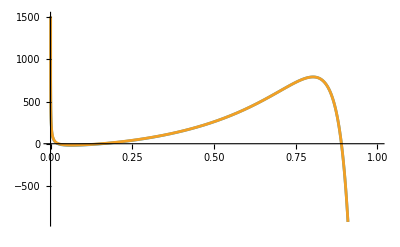

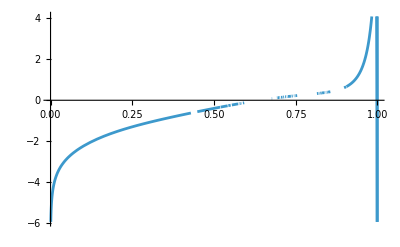

```mathematica
Plot[{
c2ns2[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3},
c2ns2appr[x]/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3]}
},{x,0,1}]
Plot[
(c2ns2[x]-c2ns2appr[x])/.{nf->3,DiracDelta[x]->0,Zeta2->Zeta[2],Zeta3->Zeta[3],CF->4/3,CA->3}
,{x,0,1}]
```

This seems to match! Now let us rewrite the coefficient function c2ns2 in form that we can put into openQCDrad...

```mathematica
c2ns2x=Collect[c2ns2[x],
{1/(1-x),DiracDelta[1-x],nf}]/.HPL[a_List,x_]:>myHPL[HPLMtoA[a],x]/.myHPL[a_List,x_]:>With[{n=Length[a]},Symbol["HPL"<>ToString[n]][Sequence@@a,x]];
c2ns2xforcode=c2ns2x/.{
x->z
}
CForm[c2ns2xforcode]
```

1/4 CF^2 (-93-209 z)+1/36 CA CF (139+3159 z)-4/5 CF^2 (7+13 z) Zeta2-4 CF^2 (1-19 z) Zeta3+(CF^2 (331/8+69 Zeta2+6 Zeta2^2-78 Zeta3)-CA CF (5465/72+(251 Zeta2)/3-(71 Zeta2^2)/5-(140 Zeta3)/3)+CF nf (457/36+(38 Zeta2)/3+(4 Zeta3)/3)) DiracDelta[-1+z]+(8 CF (-CA/2+CF) (-1+2 z) (1-HPL1[0,z]))/(5 (-2+z))-1/2 CF^2 (43+63 z) HPL1[0,z]+1/6 CA CF (71+323 z) HPL1[0,z]+1/2 CF^2 (59-109 z) HPL1[1,z]-17/6 CA CF (5-19 z) HPL1[1,z]+296/5 CF (-CA/2+CF) HPL2[-1,0,z]+(8 CF (-CA/2+CF) (1-1/z) (-1-2 z) HPL2[-1,0,z])/(5 (-2-z))+136/5 CF (-CA/2+CF) z HPL2[-1,0,z]+72/5 CF (-CA/2+CF) (1-z) (1+2 z+2 z^2) HPL2[-1,0,z]-72/5 CF (-CA/2+CF) (1-2 z+2 z^2) (-1-HPL1[0,z]+(1+z) (Zeta2-HPL2[0,0,z]))-4/5 CA CF (9+16 z) (Zeta2-HPL2[0,0,z])+1/5 CF^2 (33+37 z) HPL2[0,0,z]+2 CF^2 (5+9 z) (2 HPL2[0,1,z]+HPL2[1,1,z])+nf (1/18 CF (-23-243 z)-1/3 CF (7+19 z) HPL1[0,z]-1/3 CF (1+13 z) HPL1[1,z]+1/54 CF (-247+144 Zeta2-342 HPL1[0,z]-174 HPL1[1,z]-180 HPL2[0,0,z]-144 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z])-1/54 CF z (247-144 Zeta2+342 HPL1[0,z]+174 HPL1[1,z]+180 HPL2[0,0,z]+144 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z]))-8 CF (-CA/2+CF) (1+5 z) (Zeta2 HPL1[-1,z]+2 HPL3[-1,-1,0,z]-HPL3[-1,0,0,z])+16 CF^2 HPL3[0,-1,0,z]-8 CA CF (5 z Zeta3+HPL3[0,-1,0,z])+4 CF (-CA/2+CF) (-1+z+2/(1+z)) (7 Zeta3-8 Zeta2 HPL1[-1,z]-2 HPL1[0,z]+2 Zeta2 HPL1[0,z]-8 HPL3[-1,-1,0,z]+10 HPL3[-1,0,0,z]+4 HPL3[-1,0,1,z]+6 HPL3[0,-1,0,z]-3 HPL3[0,0,0,z]-2 HPL3[0,0,1,z])+2 CF^2 (1+z) (-4 Zeta2 HPL1[0,z]+7 HPL2[1,0,z]+5 HPL3[0,0,0,z]+4 HPL3[0,0,1,z]+2 HPL3[0,1,0,z]+2 HPL3[0,1,1,z])+8 CF (-CA/2+CF) (1-5 z) (-Zeta2 HPL1[1,z]+HPL3[1,0,0,z])+1/108 CA CF (3155-1584 Zeta2-216 Zeta3+4302 HPL1[0,z]-432 Zeta2 HPL1[0,z]+2202 HPL1[1,z]-1296 Zeta2 HPL1[1,z]+1980 HPL2[0,0,z]+1584 HPL2[0,1,z]+792 HPL2[1,0,z]+792 HPL2[1,1,z]+1296 HPL3[0,-1,0,z]+648 HPL3[0,0,0,z]+432 HPL3[0,0,1,z]+864 HPL3[1,0,0,z]+432 HPL3[1,0,1,z]-432 HPL3[1,1,0,z])-1/108 CA CF z (-3155+1584 Zeta2+216 Zeta3-4302 HPL1[0,z]+432 Zeta2 HPL1[0,z]-2202 HPL1[1,z]+1296 Zeta2 HPL1[1,z]-1980 HPL2[0,0,z]-1584 HPL2[0,1,z]-792 HPL2[1,0,z]-792 HPL2[1,1,z]-1296 HPL3[0,-1,0,z]-648 HPL3[0,0,0,z]-432 HPL3[0,0,1,z]-864 HPL3[1,0,0,z]-432 HPL3[1,0,1,z]+432 HPL3[1,1,0,z])+1/(1-z)(1/27 CF nf (247-144 Zeta2+342 HPL1[0,z]+174 HPL1[1,z]+180 HPL2[0,0,z]+144 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL1[0,z]+432 Zeta2 HPL1[0,z]-2202 HPL1[1,z]+1296 Zeta2 HPL1[1,z]-1980 HPL2[0,0,z]-1584 HPL2[0,1,z]-792 HPL2[1,0,z]-792 HPL2[1,1,z]-1296 HPL3[0,-1,0,z]-648 HPL3[0,0,0,z]-432 HPL3[0,0,1,z]-864 HPL3[1,0,0,z]-432 HPL3[1,0,1,z]+432 HPL3[1,1,0,z])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL1[0,z]+96 Zeta2 HPL1[0,z]+54 HPL1[1,z]+32 Zeta2 HPL1[1,z]-12 HPL2[0,0,z]-48 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z]+96 HPL3[0,-1,0,z]-32 HPL3[0,0,0,z]-96 HPL3[0,0,1,z]-96 HPL3[0,1,0,z]-112 HPL3[0,1,1,z]-48 HPL3[1,0,0,z]-96 HPL3[1,0,1,z]-128 HPL3[1,1,0,z]-96 HPL3[1,1,1,z]))-1/4 CF^2 z (51+48 Zeta2+128 Zeta3+122 HPL1[0,z]+96 Zeta2 HPL1[0,z]+54 HPL1[1,z]+32 Zeta2 HPL1[1,z]-12 HPL2[0,0,z]-48 HPL2[0,1,z]-72 HPL2[1,0,z]-72 HPL2[1,1,z]+96 HPL3[0,-1,0,z]-32 HPL3[0,0,0,z]-96 HPL3[0,0,1,z]-96 HPL3[0,1,0,z]-112 HPL3[0,1,1,z]-48 HPL3[1,0,0,z]-96 HPL3[1,0,1,z]-128 HPL3[1,1,0,z]-96 HPL3[1,1,1,z])+1/4 CF^2 (-51-48 Zeta2-128 Zeta3-122 HPL1[0,z]-96 Zeta2 HPL1[0,z]-54 HPL1[1,z]-32 Zeta2 HPL1[1,z]+12 HPL2[0,0,z]+48 HPL2[0,1,z]+72 HPL2[1,0,z]+72 HPL2[1,1,z]-96 HPL3[0,-1,0,z]+32 HPL3[0,0,0,z]+96 HPL3[0,0,1,z]+96 HPL3[0,1,0,z]+112 HPL3[0,1,1,z]+48 HPL3[1,0,0,z]+96 HPL3[1,0,1,z]+128 HPL3[1,1,0,z]+96 HPL3[1,1,1,z])

(Power(CF,2)*(-93 - 209*z))/4. + (CA*CF*(139 + 3159*z))/36. - (4*Power(CF,2)*(7 + 13*z)*Zeta2)/5. - 4*Power(CF,2)*(1 - 19*z)*Zeta3 + 
   (Power(CF,2)*(41.375 + 69*Zeta2 + 6*Power(Zeta2,2) - 78*Zeta3) - CA*CF*(75.90277777777777 + (251*Zeta2)/3. - (71*Power(Zeta2,2))/5. - (140*Zeta3)/3.) + 
      CF*nf*(12.694444444444445 + (38*Zeta2)/3. + (4*Zeta3)/3.))*DiracDelta(-1 + z) + (8*CF*(-0.5*CA + CF)*(-1 + 2*z)*(1 - HPL1(0,z)))/(5.*(-2 + z)) - 
   (Power(CF,2)*(43 + 63*z)*HPL1(0,z))/2. + (CA*CF*(71 + 323*z)*HPL1(0,z))/6. + (Power(CF,2)*(59 - 109*z)*HPL1(1,z))/2. - (17*CA*CF*(5 - 19*z)*HPL1(1,z))/6. + 
   (296*CF*(-0.5*CA + CF)*HPL2(-1,0,z))/5. + (8*CF*(-0.5*CA + CF)*(1 - 1/z)*(-1 - 2*z)*HPL2(-1,0,z))/(5.*(-2 - z)) + (136*CF*(-0.5*CA + CF)*z*HPL2(-1,0,z))/5. + 
   (72*CF*(-0.5*CA + CF)*(1 - z)*(1 + 2*z + 2*Power(z,2))*HPL2(-1,0,z))/5. - 
   (72*CF*(-0.5*CA + CF)*(1 - 2*z + 2*Power(z,2))*(-1 - HPL1(0,z) + (1 + z)*(Zeta2 - HPL2(0,0,z))))/5. - (4*CA*CF*(9 + 16*z)*(Zeta2 - HPL2(0,0,z)))/5. + 
   (Power(CF,2)*(33 + 37*z)*HPL2(0,0,z))/5. + 2*Power(CF,2)*(5 + 9*z)*(2*HPL2(0,1,z) + HPL2(1,1,z)) + 
   nf*((CF*(-23 - 243*z))/18. - (CF*(7 + 19*z)*HPL1(0,z))/3. - (CF*(1 + 13*z)*HPL1(1,z))/3. + 
      (CF*(-247 + 144*Zeta2 - 342*HPL1(0,z) - 174*HPL1(1,z) - 180*HPL2(0,0,z) - 144*HPL2(0,1,z) - 72*HPL2(1,0,z) - 72*HPL2(1,1,z)))/54. - 
      (CF*z*(247 - 144*Zeta2 + 342*HPL1(0,z) + 174*HPL1(1,z) + 180*HPL2(0,0,z) + 144*HPL2(0,1,z) + 72*HPL2(1,0,z) + 72*HPL2(1,1,z)))/54.) - 
   8*CF*(-0.5*CA + CF)*(1 + 5*z)*(Zeta2*HPL1(-1,z) + 2*HPL3(-1,-1,0,z) - HPL3(-1,0,0,z)) + 16*Power(CF,2)*HPL3(0,-1,0,z) - 8*CA*CF*(5*z*Zeta3 + HPL3(0,-1,0,z)) + 
   4*CF*(-0.5*CA + CF)*(-1 + z + 2/(1 + z))*(7*Zeta3 - 8*Zeta2*HPL1(-1,z) - 2*HPL1(0,z) + 2*Zeta2*HPL1(0,z) - 8*HPL3(-1,-1,0,z) + 10*HPL3(-1,0,0,z) + 4*HPL3(-1,0,1,z) + 
      6*HPL3(0,-1,0,z) - 3*HPL3(0,0,0,z) - 2*HPL3(0,0,1,z)) + 2*Power(CF,2)*(1 + z)*
    (-4*Zeta2*HPL1(0,z) + 7*HPL2(1,0,z) + 5*HPL3(0,0,0,z) + 4*HPL3(0,0,1,z) + 2*HPL3(0,1,0,z) + 2*HPL3(0,1,1,z)) + 
   8*CF*(-0.5*CA + CF)*(1 - 5*z)*(-(Zeta2*HPL1(1,z)) + HPL3(1,0,0,z)) + 
   (CA*CF*(3155 - 1584*Zeta2 - 216*Zeta3 + 4302*HPL1(0,z) - 432*Zeta2*HPL1(0,z) + 2202*HPL1(1,z) - 1296*Zeta2*HPL1(1,z) + 1980*HPL2(0,0,z) + 1584*HPL2(0,1,z) + 
        792*HPL2(1,0,z) + 792*HPL2(1,1,z) + 1296*HPL3(0,-1,0,z) + 648*HPL3(0,0,0,z) + 432*HPL3(0,0,1,z) + 864*HPL3(1,0,0,z) + 432*HPL3(1,0,1,z) - 432*HPL3(1,1,0,z)))/108.\
    - (CA*CF*z*(-3155 + 1584*Zeta2 + 216*Zeta3 - 4302*HPL1(0,z) + 432*Zeta2*HPL1(0,z) - 2202*HPL1(1,z) + 1296*Zeta2*HPL1(1,z) - 1980*HPL2(0,0,z) - 1584*HPL2(0,1,z) - 
        792*HPL2(1,0,z) - 792*HPL2(1,1,z) - 1296*HPL3(0,-1,0,z) - 648*HPL3(0,0,0,z) - 432*HPL3(0,0,1,z) - 864*HPL3(1,0,0,z) - 432*HPL3(1,0,1,z) + 432*HPL3(1,1,0,z)))/108.\
    + ((CF*nf*(247 - 144*Zeta2 + 342*HPL1(0,z) + 174*HPL1(1,z) + 180*HPL2(0,0,z) + 144*HPL2(0,1,z) + 72*HPL2(1,0,z) + 72*HPL2(1,1,z)))/27. + 
      (CA*CF*(-3155 + 1584*Zeta2 + 216*Zeta3 - 4302*HPL1(0,z) + 432*Zeta2*HPL1(0,z) - 2202*HPL1(1,z) + 1296*Zeta2*HPL1(1,z) - 1980*HPL2(0,0,z) - 1584*HPL2(0,1,z) - 
           792*HPL2(1,0,z) - 792*HPL2(1,1,z) - 1296*HPL3(0,-1,0,z) - 648*HPL3(0,0,0,z) - 432*HPL3(0,0,1,z) - 864*HPL3(1,0,0,z) - 432*HPL3(1,0,1,z) + 432*HPL3(1,1,0,z)))/
       54. + (Power(CF,2)*(51 + 48*Zeta2 + 128*Zeta3 + 122*HPL1(0,z) + 96*Zeta2*HPL1(0,z) + 54*HPL1(1,z) + 32*Zeta2*HPL1(1,z) - 12*HPL2(0,0,z) - 48*HPL2(0,1,z) - 
           72*HPL2(1,0,z) - 72*HPL2(1,1,z) + 96*HPL3(0,-1,0,z) - 32*HPL3(0,0,0,z) - 96*HPL3(0,0,1,z) - 96*HPL3(0,1,0,z) - 112*HPL3(0,1,1,z) - 48*HPL3(1,0,0,z) - 
           96*HPL3(1,0,1,z) - 128*HPL3(1,1,0,z) - 96*HPL3(1,1,1,z)))/2.)/(1 - z) - 
   (Power(CF,2)*z*(51 + 48*Zeta2 + 128*Zeta3 + 122*HPL1(0,z) + 96*Zeta2*HPL1(0,z) + 54*HPL1(1,z) + 32*Zeta2*HPL1(1,z) - 12*HPL2(0,0,z) - 48*HPL2(0,1,z) - 72*HPL2(1,0,z) - 
        72*HPL2(1,1,z) + 96*HPL3(0,-1,0,z) - 32*HPL3(0,0,0,z) - 96*HPL3(0,0,1,z) - 96*HPL3(0,1,0,z) - 112*HPL3(0,1,1,z) - 48*HPL3(1,0,0,z) - 96*HPL3(1,0,1,z) - 
        128*HPL3(1,1,0,z) - 96*HPL3(1,1,1,z)))/4. + (Power(CF,2)*(-51 - 48*Zeta2 - 128*Zeta3 - 122*HPL1(0,z) - 96*Zeta2*HPL1(0,z) - 54*HPL1(1,z) - 32*Zeta2*HPL1(1,z) + 
        12*HPL2(0,0,z) + 48*HPL2(0,1,z) + 72*HPL2(1,0,z) + 72*HPL2(1,1,z) - 96*HPL3(0,-1,0,z) + 32*HPL3(0,0,0,z) + 96*HPL3(0,0,1,z) + 96*HPL3(0,1,0,z) + 
        112*HPL3(0,1,1,z) + 48*HPL3(1,0,0,z) + 96*HPL3(1,0,1,z) + 128*HPL3(1,1,0,z) + 96*HPL3(1,1,1,z)))/4.

For convenience...

```mathematica
Collect[c2ns2[x],{1/(1-x),DiracDelta[1-x],nf}]
c2ns2plus=1/(1-x)(1/27 CF nf (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x]));
c2ns2reg=1/4 CF^2 (-93-209 x)+1/36 CA CF (139+3159 x)-4/5 CF^2 (7+13 x) Zeta2-4 CF^2 (1-19 x) Zeta3+(8 CF (-CA/2+CF) (-1+2 x) (1-HPL[{0},x]))/(5 (-2+x))-1/2 CF^2 (43+63 x) HPL[{0},x]+1/6 CA CF (71+323 x) HPL[{0},x]+1/2 CF^2 (59-109 x) HPL[{1},x]-17/6 CA CF (5-19 x) HPL[{1},x]+16 CF^2 HPL[{-2,0},x]-8 CA CF (5 x Zeta3+HPL[{-2,0},x])+296/5 CF (-CA/2+CF) HPL[{-1,0},x]+(8 CF (-CA/2+CF) (1-1/x) (-1-2 x) HPL[{-1,0},x])/(5 (-2-x))+136/5 CF (-CA/2+CF) x HPL[{-1,0},x]+72/5 CF (-CA/2+CF) (1-x) (1+2 x+2 x^2) HPL[{-1,0},x]-72/5 CF (-CA/2+CF) (1-2 x+2 x^2) (-1-HPL[{0},x]+(1+x) (Zeta2-HPL[{0,0},x]))-4/5 CA CF (9+16 x) (Zeta2-HPL[{0,0},x])+1/5 CF^2 (33+37 x) HPL[{0,0},x]+2 CF^2 (5+9 x) (2 HPL[{2},x]+HPL[{1,1},x])+nf (1/18 CF (-23-243 x)-1/3 CF (7+19 x) HPL[{0},x]-1/3 CF (1+13 x) HPL[{1},x]+1/54 CF (-247+144 Zeta2-342 HPL[{0},x]-174 HPL[{1},x]-144 HPL[{2},x]-180 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x])-1/54 CF x (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]))-8 CF (-CA/2+CF) (1+5 x) (Zeta2 HPL[{-1},x]+2 HPL[{-1,-1,0},x]-HPL[{-1,0,0},x])+4 CF (-CA/2+CF) (-1+x+2/(1+x)) (7 Zeta3-8 Zeta2 HPL[{-1},x]-2 HPL[{0},x]+2 Zeta2 HPL[{0},x]-2 HPL[{3},x]+6 HPL[{-2,0},x]+4 HPL[{-1,2},x]-8 HPL[{-1,-1,0},x]+10 HPL[{-1,0,0},x]-3 HPL[{0,0,0},x])+2 CF^2 (1+x) (-4 Zeta2 HPL[{0},x]+4 HPL[{3},x]+7 HPL[{1,0},x]+2 HPL[{2,0},x]+2 HPL[{2,1},x]+5 HPL[{0,0,0},x])+8 CF (-CA/2+CF) (1-5 x) (-Zeta2 HPL[{1},x]+HPL[{1,0,0},x])+1/108 CA CF (3155-1584 Zeta2-216 Zeta3+4302 HPL[{0},x]-432 Zeta2 HPL[{0},x]+2202 HPL[{1},x]-1296 Zeta2 HPL[{1},x]+1584 HPL[{2},x]+432 HPL[{3},x]+1296 HPL[{-2,0},x]+1980 HPL[{0,0},x]+792 HPL[{1,0},x]+792 HPL[{1,1},x]+432 HPL[{1,2},x]+648 HPL[{0,0,0},x]+864 HPL[{1,0,0},x]-432 HPL[{1,1,0},x])-1/108 CA CF x (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])-1/4 CF^2 x (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x])+1/4 CF^2 (-51-48 Zeta2-128 Zeta3-122 HPL[{0},x]-96 Zeta2 HPL[{0},x]-54 HPL[{1},x]-32 Zeta2 HPL[{1},x]+48 HPL[{2},x]+96 HPL[{3},x]-96 HPL[{-2,0},x]+12 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]+96 HPL[{1,2},x]+96 HPL[{2,0},x]+112 HPL[{2,1},x]+32 HPL[{0,0,0},x]+48 HPL[{1,0,0},x]+128 HPL[{1,1,0},x]+96 HPL[{1,1,1},x]);
```

1/4 CF^2 (-93-209 x)+1/36 CA CF (139+3159 x)-4/5 CF^2 (7+13 x) Zeta2-4 CF^2 (1-19 x) Zeta3+(CF^2 (331/8+69 Zeta2+6 Zeta2^2-78 Zeta3)-CA CF (5465/72+(251 Zeta2)/3-(71 Zeta2^2)/5-(140 Zeta3)/3)+CF nf (457/36+(38 Zeta2)/3+(4 Zeta3)/3)) DiracDelta[-1+x]+(8 CF (-CA/2+CF) (-1+2 x) (1-HPL[{0},x]))/(5 (-2+x))-1/2 CF^2 (43+63 x) HPL[{0},x]+1/6 CA CF (71+323 x) HPL[{0},x]+1/2 CF^2 (59-109 x) HPL[{1},x]-17/6 CA CF (5-19 x) HPL[{1},x]+16 CF^2 HPL[{-2,0},x]-8 CA CF (5 x Zeta3+HPL[{-2,0},x])+296/5 CF (-CA/2+CF) HPL[{-1,0},x]+(8 CF (-CA/2+CF) (1-1/x) (-1-2 x) HPL[{-1,0},x])/(5 (-2-x))+136/5 CF (-CA/2+CF) x HPL[{-1,0},x]+72/5 CF (-CA/2+CF) (1-x) (1+2 x+2 x^2) HPL[{-1,0},x]-72/5 CF (-CA/2+CF) (1-2 x+2 x^2) (-1-HPL[{0},x]+(1+x) (Zeta2-HPL[{0,0},x]))-4/5 CA CF (9+16 x) (Zeta2-HPL[{0,0},x])+1/5 CF^2 (33+37 x) HPL[{0,0},x]+2 CF^2 (5+9 x) (2 HPL[{2},x]+HPL[{1,1},x])+nf (1/18 CF (-23-243 x)-1/3 CF (7+19 x) HPL[{0},x]-1/3 CF (1+13 x) HPL[{1},x]+1/54 CF (-247+144 Zeta2-342 HPL[{0},x]-174 HPL[{1},x]-144 HPL[{2},x]-180 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x])-1/54 CF x (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]))-8 CF (-CA/2+CF) (1+5 x) (Zeta2 HPL[{-1},x]+2 HPL[{-1,-1,0},x]-HPL[{-1,0,0},x])+4 CF (-CA/2+CF) (-1+x+2/(1+x)) (7 Zeta3-8 Zeta2 HPL[{-1},x]-2 HPL[{0},x]+2 Zeta2 HPL[{0},x]-2 HPL[{3},x]+6 HPL[{-2,0},x]+4 HPL[{-1,2},x]-8 HPL[{-1,-1,0},x]+10 HPL[{-1,0,0},x]-3 HPL[{0,0,0},x])+2 CF^2 (1+x) (-4 Zeta2 HPL[{0},x]+4 HPL[{3},x]+7 HPL[{1,0},x]+2 HPL[{2,0},x]+2 HPL[{2,1},x]+5 HPL[{0,0,0},x])+8 CF (-CA/2+CF) (1-5 x) (-Zeta2 HPL[{1},x]+HPL[{1,0,0},x])+1/108 CA CF (3155-1584 Zeta2-216 Zeta3+4302 HPL[{0},x]-432 Zeta2 HPL[{0},x]+2202 HPL[{1},x]-1296 Zeta2 HPL[{1},x]+1584 HPL[{2},x]+432 HPL[{3},x]+1296 HPL[{-2,0},x]+1980 HPL[{0,0},x]+792 HPL[{1,0},x]+792 HPL[{1,1},x]+432 HPL[{1,2},x]+648 HPL[{0,0,0},x]+864 HPL[{1,0,0},x]-432 HPL[{1,1,0},x])-1/108 CA CF x (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])+1/(1-x)(1/27 CF nf (247-144 Zeta2+342 HPL[{0},x]+174 HPL[{1},x]+144 HPL[{2},x]+180 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x])+1/54 CA CF (-3155+1584 Zeta2+216 Zeta3-4302 HPL[{0},x]+432 Zeta2 HPL[{0},x]-2202 HPL[{1},x]+1296 Zeta2 HPL[{1},x]-1584 HPL[{2},x]-432 HPL[{3},x]-1296 HPL[{-2,0},x]-1980 HPL[{0,0},x]-792 HPL[{1,0},x]-792 HPL[{1,1},x]-432 HPL[{1,2},x]-648 HPL[{0,0,0},x]-864 HPL[{1,0,0},x]+432 HPL[{1,1,0},x])+1/2 CF^2 (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x]))-1/4 CF^2 x (51+48 Zeta2+128 Zeta3+122 HPL[{0},x]+96 Zeta2 HPL[{0},x]+54 HPL[{1},x]+32 Zeta2 HPL[{1},x]-48 HPL[{2},x]-96 HPL[{3},x]+96 HPL[{-2,0},x]-12 HPL[{0,0},x]-72 HPL[{1,0},x]-72 HPL[{1,1},x]-96 HPL[{1,2},x]-96 HPL[{2,0},x]-112 HPL[{2,1},x]-32 HPL[{0,0,0},x]-48 HPL[{1,0,0},x]-128 HPL[{1,1,0},x]-96 HPL[{1,1,1},x])+1/4 CF^2 (-51-48 Zeta2-128 Zeta3-122 HPL[{0},x]-96 Zeta2 HPL[{0},x]-54 HPL[{1},x]-32 Zeta2 HPL[{1},x]+48 HPL[{2},x]+96 HPL[{3},x]-96 HPL[{-2,0},x]+12 HPL[{0,0},x]+72 HPL[{1,0},x]+72 HPL[{1,1},x]+96 HPL[{1,2},x]+96 HPL[{2,0},x]+112 HPL[{2,1},x]+32 HPL[{0,0,0},x]+48 HPL[{1,0,0},x]+128 HPL[{1,1,0},x]+96 HPL[{1,1,1},x])